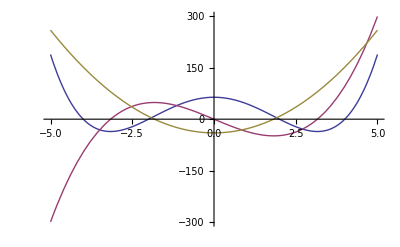

```mathematica
a6=1;
a5=0;
a4=0;
a3=0;
a2=0;
a1=0;
a0=0;
F0[x_]=(x-2)*(x+2)*(x-4)*(x+4);
F1[x_]=D[F0[x],x];
F2[x_]=D[F1[x],x];
Plot[{F0[x], F1[x], F2[x]}, {x,-5,5}]
```